```mathematica
dof[m_,n_]:=Simplify[(n(n-1)/2)-((n-m)(n-m-1)/2)]
```

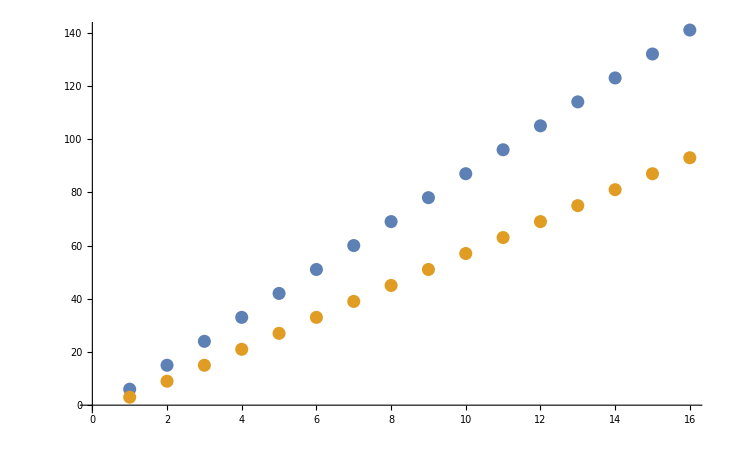

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[dof[m,n],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
rot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[tt],"=",ToString[t],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Cos[tt];mm[[i,j]]=-Sin[tt];mm[[j,i]]=Sin[tt];mm[[j,j]]=Cos[tt];mm)]
```

```mathematica
rot[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[x[2,3]] | -Sin[x[2,3]] | 0
0 | Sin[x[2,3]] | Cos[x[2,3]] | 0
0 | 0 | 0 | 1)

```mathematica
rot2[x_,i_,j_,n_]:=Module[{mm,xx},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[xx],"=",ToString[x],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Sqrt[1-xx];mm[[i,j]]=-Sqrt[xx];mm[[j,i]]=Sqrt[xx];mm[[j,j]]=Sqrt[1-xx];mm)]
```

```mathematica
rot2[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | √(1-x[2,3]) | -√x[2,3] | 0
0 | √x[2,3] | √(1-x[2,3]) | 0
0 | 0 | 0 | 1)

```mathematica
fullRotMat[t_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot[t,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat[t,1,3]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | Cos[t[1,3]])

```mathematica
fullRotMat2[x_,m_,n_]:=l
```

```mathematica
fullRotMat2[t,1,3]//MatrixForm
```

(√(1-t[1,2]) √(1-t[1,3]) | -√t[1,2] | -√(1-t[1,2]) √t[1,3]
√t[1,2] √(1-t[1,3]) | √(1-t[1,2]) | -√t[1,2] √t[1,3]
√t[1,3] | 0 | √(1-t[1,3]))

```mathematica
sumRows[mm_,m_,n_]:=Table[Sum[Map[Abs,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
makeEqn[ms_,n_]:=Table[o==ms[[i]],{i,1,n}]
```

```mathematica
trySolve[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRows[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
sumRowsNoAbs[mm_,m_,n_]:=Table[Sum[mm[[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
trySolveNoAbs[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRowsNoAbs[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
makeVars[x_,m_,n_]:=Flatten[Table[Table[{x[i,j]},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeSub[t_,x_,m_,n_]:=Flatten[Table[Table[{Sin[t[i,j]]->Sqrt[x[i,j]],Cos[t[i,j]]->Sqrt[1-x[i,j]]},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x_,m_,n_,xmin_,xmax_]:=Flatten[Table[Table[{xmin<=x[i,j]<=xmax},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x,2,3,0,1]
```

{0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[2,3]≤1}

```mathematica
makeCon[t,2,3,0,2Pi]
```

{0≤t[1,2]≤2 π,0≤t[1,3]≤2 π,0≤t[2,3]≤2 π}

```mathematica
mm=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mmzero=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm2=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm[[1,2]]=fullRotMat[t,1,2];mm2[[1,2]]=fullRotMat2[x,1,2];mm[[1,2]]//MatrixForm
mm2[[1,2]]//MatrixForm
```

(Cos[t[1,2]] | -Sin[t[1,2]]
Sin[t[1,2]] | Cos[t[1,2]])

(√(1-x[1,2]) | -√x[1,2]
√x[1,2] | √(1-x[1,2]))

```mathematica
mm12=mm[[1,2]];
```

```mathematica
FullSimplify[mm[[1,2]]/.{t[1,2]->Pi/4}]//MatrixForm
```

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

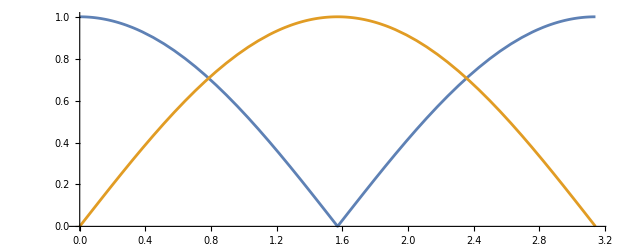

```mathematica
Plot[{Abs[mm12[[1,1]]],Abs[mm12[[2,1]]]},{t[1,2],0,Pi},AspectRatio->Automatic]
```

```mathematica
gradmm121={D[mm12[[1,1]],t[1,2]]};gradmm121//MatrixForm
```

(-Sin[t[1,2]])

```mathematica
gradmm122={D[mm12[[2,1]],t[1,2]]};gradmm122//MatrixForm
```

(Cos[t[1,2]])

```mathematica
mm[[2,3]]=fullRotMat[t,2,3];mm2[[2,3]]=fullRotMat2[x,2,3];mm[[2,3]]//MatrixForm
mm2[[2,3]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]]
Sin[t[1,3]] | Cos[t[1,3]] Sin[t[2,3]] | Cos[t[1,3]] Cos[t[2,3]])

(√(1-x[1,2]) √(1-x[1,3]) | -√x[1,2] √(1-x[2,3])-√(1-x[1,2]) √x[1,3] √x[2,3] | -√(1-x[1,2]) √x[1,3] √(1-x[2,3])+√x[1,2] √x[2,3]
√x[1,2] √(1-x[1,3]) | √(1-x[1,2]) √(1-x[2,3])-√x[1,2] √x[1,3] √x[2,3] | -√x[1,2] √x[1,3] √(1-x[2,3])-√(1-x[1,2]) √x[2,3]
√x[1,3] | √(1-x[1,3]) √x[2,3] | √(1-x[1,3]) √(1-x[2,3]))

```mathematica
mm[[2,3]]/.{t[1,2]->Pi/4,t[1,3]->0}//MatrixForm
```

(1/(√2) | -Cos[t[2,3]]/(√2) | Sin[t[2,3]]/(√2)
1/(√2) | Cos[t[2,3]]/(√2) | -Sin[t[2,3]]/(√2)
0 | Sin[t[2,3]] | Cos[t[2,3]])

```mathematica
mm23 = mm[[2,3]];
```

```mathematica
Solve[(mm23[[2,1]]+mm23[[2,2]]==mm23[[3,1]]+mm23[[3,2]])/.{t[1,2]->Pi/4,t[1,3]->0},Assumptions->{0<=t[2,3]<=Pi/2}]
```

{{t[2,3]→2 ArcTan[1/(√2)]}}

```mathematica
FullSimplify[mm[[2,3]]/.{t[1,2]->Pi/4,t[1,3]->0,t[2,3]->2ArcTan[1/Sqrt[2]]}]//MatrixForm
```

(1/(√2) | -1/(3 √2) | 2/3
1/(√2) | 1/(3 √2) | -2/3
0 | (2 √2)/3 | 1/3)

```mathematica
ContourPlot3D[Abs[mm23[[1,1]]]+Abs[mm23[[1,2]]],{t[1,2],0,Pi/2},{t[1,3],0,Pi/2},{t[2,3],0,Pi/2},Contours->{0.1,0.5,1.0},ContourStyle->{Yellow,Green,Cyan},Mesh->None,MaxRecursion->1,PlotPoints->20]
```

-Graphics3D-

```mathematica
ContourPlot3D[Abs[mm23[[2,1]]]+Abs[mm23[[2,2]]],{t[1,2],0,Pi/2},{t[1,3],0,Pi/2},{t[2,3],0,Pi/2},Contours->{0.1,0.5,1.0},ContourStyle->{Yellow,Green,Cyan},Mesh->None,MaxRecursion->1,PlotPoints->20]
```

-Graphics3D-

```mathematica
ContourPlot3D[Abs[mm23[[3,1]]]+Abs[mm23[[3,2]]],{t[1,2],0,Pi/2},{t[1,3],0,Pi/2},{t[2,3],0,Pi/2},Contours->{0.1,0.5,1.0},ContourStyle->{Yellow,Green,Cyan},Mesh->None,MaxRecursion->1,PlotPoints->20]
```

-Graphics3D-

```mathematica
gradmm231={D[mm23[[1,1]]-mm23[[1,2]],t[1,2]],D[mm23[[1,1]]-mm23[[1,2]],t[1,3]],D[mm23[[1,1]]-mm23[[1,2]],t[2,3]]};gradmm231//MatrixForm
```

(Cos[t[1,2]] Cos[t[2,3]]-Cos[t[1,3]] Sin[t[1,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]
-Cos[t[1,2]] Sin[t[1,3]]+Cos[t[1,2]] Cos[t[1,3]] Sin[t[2,3]]
Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]-Sin[t[1,2]] Sin[t[2,3]])

```mathematica
gradmm232={D[mm23[[2,1]]+mm23[[2,2]],t[1,2]],D[mm23[[2,1]]+mm23[[2,2]],t[1,3]],D[mm23[[2,1]]+mm23[[2,2]],t[2,3]]};gradmm232//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]]-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]
-Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,3]] Sin[t[1,2]] Sin[t[2,3]]
-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]])

```mathematica
gradmm233={D[mm23[[3,1]]+mm23[[3,2]],t[1,2]],D[mm23[[3,1]]+mm23[[3,2]],t[1,3]],D[mm23[[3,1]]+mm23[[3,2]],t[2,3]]};gradmm233//MatrixForm
```

(0
Cos[t[1,3]]-Sin[t[1,3]] Sin[t[2,3]]
Cos[t[1,3]] Cos[t[2,3]])

```mathematica
FullSimplify[gradmm231/.{t[1,2]->Pi/4,t[1,3]->0,t[2,3]->2ArcTan[1/Sqrt[2]]}]
```

{-(√2)/3,2/3,-2/3}

```mathematica
FullSimplify[gradmm232/.{t[1,2]->Pi/4,t[1,3]->0,t[2,3]->2ArcTan[1/Sqrt[2]]}]
```

{(√2)/3,-2/3,-2/3}

```mathematica
FullSimplify[gradmm233/.{t[1,2]->Pi/4,t[1,3]->0,t[2,3]->2ArcTan[1/Sqrt[2]]}]
```

{0,1,1/3}

```mathematica
eps=0.0005;sc=0.0004;ptmin={Pi/4,0,2ArcTan[1/Sqrt[2]]};Show[ContourPlot3D[Max[Abs[mm23[[1,1]]]+Abs[mm23[[1,2]]],Abs[mm23[[2,1]]]+Abs[mm23[[2,2]]],Abs[mm23[[3,1]]]+Abs[mm23[[3,2]]]],{t[1,2],ptmin[[1]]-eps,ptmin[[1]]+eps},{t[1,3],ptmin[[2]]-eps,ptmin[[2]]+eps},{t[2,3],ptmin[[3]]-eps,ptmin[[3]]+eps},Contours->{0.943},ContourStyle->Directive[Opacity[0.5],Gray],Mesh->None,MaxRecursion->2,PlotPoints->20],Graphics3D[{Brown,Sphere[ptmin,0.00005]}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{ptmin,ptmin+sc{-(√2)/3,2/3,-2/3}},0.00001]],Green,Arrowheads[0.05],Arrow[Tube[{ptmin,ptmin+sc{(√2)/3,-2/3,-2/3}},0.00001]],Blue,Arrowheads[0.05],Arrow[Tube[{ptmin,ptmin+sc{0,1,1/3}},0.00001]]},AspectRatio->1]]
```

-Graphics3D-

```mathematica
eps=0.04;pt={Pi/4,0,2ArcTan[1/Sqrt[2]]};
val=0.95;res=Timing[Show[ContourPlot3D[Max[Abs[mm23[[1,1]]]+Abs[mm23[[1,2]]],Abs[mm23[[2,1]]]+Abs[mm23[[2,2]]],Abs[mm23[[3,1]]]+Abs[mm23[[3,2]]]],{t[1,2],pt[[1]]-eps,pt[[1]]+eps},{t[1,3],pt[[2]]-eps,pt[[2]]+eps},{t[2,3],pt[[3]]-eps,pt[[3]]+eps},Contours->{val},ContourStyle->Directive[Opacity[0.3],Red],Mesh->None,MaxRecursion->1,PlotPoints->30],Graphics3D[{Brown,Sphere[ptmin,0.002]}]]];res[[1]]
res[[2]]
```

3.98121

-Graphics3D-

```mathematica
AbsSqrt[x_,eps_]:=Sqrt[x^2+eps^2]
```

```mathematica
MaxSqrt2[x_,y_,eps_]:=(x+y+AbsSqrt[x-y,eps])/2
```

```mathematica
MaxSqrt3[x_,y_,z_,eps_]:=MaxSqrt2[MaxSqrt2[x,y,eps],z,eps]
```

```mathematica
eps=0.04;eps2=0.0001;
eps3=0.0003;pt={Pi/4,0,2ArcTan[1/Sqrt[2]]};
val=0.95;res=Timing[Show[ContourPlot3D[MaxSqrt3[AbsSqrt[mm23⟦1,1⟧,eps2]+AbsSqrt[mm23⟦1,2⟧,eps2],AbsSqrt[mm23⟦2,1⟧,eps2]+AbsSqrt[mm23⟦2,2⟧,eps2],AbsSqrt[mm23⟦3,1⟧,eps2]+AbsSqrt[mm23⟦3,2⟧,eps2],eps3],{t[1,2],pt⟦1⟧-eps,pt⟦1⟧+eps},{t[1,3],pt⟦2⟧-eps,pt⟦2⟧+eps},{t[2,3],pt⟦3⟧-eps,pt⟦3⟧+eps},Contours->{val},ContourStyle->Directive[Opacity[0.3],Green],Mesh->None,MaxRecursion->0,PlotPoints->30],Graphics3D[{Brown,Sphere[ptmin,0.002]}]]];res[[1]]
res[[2]]
```

2.784

-Graphics3D-

```mathematica
mm23//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]]
Sin[t[1,3]] | Cos[t[1,3]] Sin[t[2,3]] | Cos[t[1,3]] Cos[t[2,3]])

```mathematica
D[mm23,t[1,2]]//MatrixForm
```

(-Cos[t[1,3]] Sin[t[1,2]] | -Cos[t[1,2]] Cos[t[2,3]]+Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]+Cos[t[1,2]] Sin[t[2,3]]
Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]
0 | 0 | 0)

```mathematica
drot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=ConstantArray[0,{n,n}];
ToExpression[StringJoin[ToString[tt],"=",ToString[t],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=D[Cos[tt],tt];mm[[i,j]]=D[-Sin[tt],tt];mm[[j,i]]=D[Sin[tt],tt];mm[[j,j]]=D[Cos[tt],tt];mm)]
```

```mathematica
drot[t,1,2,3]//MatrixForm
```

(-Sin[t[1,2]] | -Cos[t[1,2]] | 0
Cos[t[1,2]] | -Sin[t[1,2]] | 0
0 | 0 | 0)

```mathematica
try=drot[t,1,2,3].rot[t,1,3,3].rot[t,2,3,3];try//MatrixForm
```

(-Cos[t[1,3]] Sin[t[1,2]] | -Cos[t[1,2]] Cos[t[2,3]]+Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]+Cos[t[1,2]] Sin[t[2,3]]
Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]
0 | 0 | 0)

```mathematica
D[mm23,t[1,2]]-try//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
mm23/.{t[1,2]->1.55827004,t[1,3]->-0.38701052,t[2,3]->  2.5715329}//MatrixForm
```

(0.0115996 | 0.844354 | 0.53566
0.925969 | 0.193127 | -0.324475
-0.377422 | 0.499768 | -0.779605)

```mathematica
D[mm23,t[1,2]]/.{t[1,2]->1.55827004,t[1,3]->-0.38701052,t[2,3]->  2.5715329}//MatrixForm
```

(-0.925969 | -0.193127 | 0.324475
0.0115996 | 0.844354 | 0.53566
0 | 0 | 0)

```mathematica
D[mm23,t[1,3]]/.{t[1,2]->1.55827004,t[1,3]->-0.38701052,t[2,3]->  2.5715329}//MatrixForm
```

(0.00472757 | -0.00626008 | 0.00976531
0.377392 | -0.499729 | 0.779544
0.926041 | 0.203688 | -0.31774)

```mathematica
D[mm23,t[2,3]]/.{t[1,2]->1.55827004,t[1,3]->-0.38701052,t[2,3]->  2.5715329}//MatrixForm
```

(0 | 0.53566 | -0.844354
0 | -0.324475 | -0.193127
0 | -0.779605 | -0.499768)

```mathematica
Show[Plot3D[Max[sumRows[mm[[1,3]],1,3]],{t[1,2],-Pi,0},{t[1,3],0,Pi},Mesh->None,Exclusions->None,MaxRecursion->3,PlotPoints->40],ListPointPlot3D[{{t[1,2],t[1,3],Max[sumRows[mm[[1,3]],1,3]]}/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257}},PlotStyle->{PointSize[0.02]}]]
```

-Graphics3D-

```mathematica
AbsSqrt[x_,eps_]:=Sqrt[x^2+eps^2]
```

```mathematica
dAbsSqrt[x_,eps_]:=x/AbsSqrt[x,eps]
```

```mathematica
sumRowsSqrt[mm_,m_,n_,eps_]:=Table[Sum[Map[AbsSqrt[#1,eps]&,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
dSumRowsSqrt[mm_,m_,n_,eps_]:=Table[Sum[Map[dAbsSqrt[#1,eps]&,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
MaxExp[X_,eps_]:=Module[{max},(max=0;xm=Max[X];For[i=1,i<=Length[X],i++,max=max+Exp[ (X[[i]]-xm)/eps]];eps Log[max] + xm)]
```

```mathematica
dMaxExp[X_,eps_]:=Module[{max},(sum=0;xm=0;For[i=1,i<=Length[X],i++,sum=sum+Exp[ (X[[i]]-xm)/eps]];Exp[(X-xm)/eps]/sum )]
```

```mathematica
{{t[1,2],t[1,3],MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1]}/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257}}
```

{{-1.86754,2.6681,0.85924}}

```mathematica
Show[Plot3D[MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1],{t[1,2],-Pi,0},{t[1,3],0,Pi},Mesh->None,Exclusions->None,MaxRecursion->5,PlotPoints->100],ListPointPlot3D[{{t[1,2],t[1,3],MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1]}/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257},{t[1,2],t[1,3],MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1]}/.{t[1,2]->-2.0295847895,t[1,3]->2.4048554192},{t[1,2],t[1,3],MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1]}/.{t[1,2]->-2.3561944902,t[1,3]->  2.5261129398}},PlotStyle->{PointSize[0.02]}]]
```

-Graphics3D-

```mathematica
{t[1,2],t[1,3],Max[sumRows[mm[[1,3]],1,3]]}/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257}
```

{-1.86754,2.6681,0.851082}

```mathematica
{t[1,2],t[1,3],MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1]}/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257}
```

{-1.86754,2.6681,0.85924}

```mathematica
{D[Max[sumRows[mm[[1,3]],1,3]],t[1,2]]/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257},D[Max[sumRows[mm[[1,3]],1,3]],t[1,3]]/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257}}
```

{0.260239 Abs'[0.851082],0.436069 Abs'[0.851082]}

```mathematica
{D[MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1],t[1,2]]/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257},D[MaxExp[sumRowsSqrt[mm[[1,3]],1,3,0.1],0.1],t[1,3]]/.{t[1,2]->-1.8675421567,t[1,3]->2.6680973257}}
```

{0.25018,0.406423}

```mathematica
funcSqrt=MaxExp[sumRowsSqrt[mm[[1,3]],1,3,tol],tol]
```

tol Log[ⅇ^((√(tol^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2)-Max[√(tol^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2),√(tol^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2),√(tol^2+Sin[t[1,3]]^2)])/tol)+ⅇ^((-Max[√(tol^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2),√(tol^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2),√(tol^2+Sin[t[1,3]]^2)]+√(tol^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2))/tol)+ⅇ^((-Max[√(tol^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2),√(tol^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2),√(tol^2+Sin[t[1,3]]^2)]+√(tol^2+Sin[t[1,3]]^2))/tol)]+Max[√(tol^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2),√(tol^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2),√(tol^2+Sin[t[1,3]]^2)]

```mathematica
t12=0.785398156200249;t13=0.6154797026443322;
```

```mathematica
funcSqrt/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}
```

0.695808

```mathematica
mm[[1,3]][[;;,1]]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}
```

{0.57735,0.57735,0.57735}

```mathematica
Map[AbsSqrt[#,0.1]&,mm[[1,3]][[;;,1]]]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}
```

{0.585947,0.585947,0.585947}

```mathematica
sumRowsSqrt[mm[[1,3]],1,3,tol]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}
```

{0.585947,0.585947,0.585947}

```mathematica
Max[sumRowsSqrt[mm[[1,3]],1,3,tol]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}]
```

0.585947

```mathematica
MaxExp[sumRowsSqrt[mm[[1,3]],1,3,tol],tol]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}
```

0.695808

```mathematica
D[MaxExp[sumRowsSqrt[mm[[1,3]],1,3,tol],tol],t[1,2]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}
```

-1.28779×10^-8

```mathematica
D[MaxExp[sumRowsSqrt[mm[[1,3]],1,3,tol],tol],t[1,3]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}
```

-1.61735×10^-8

```mathematica
dSumRowsSqrt[mm[[1,3]],1,3,tol]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}
```

{0.985329,0.985329,0.985329}

```mathematica
dMaxExp[sumRowsSqrt[mm[[1,3]],1,3,tol],tol]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}//MatrixForm
```

(0.333333
0.333333
0.333333)

```mathematica
Total[dMaxExp[sumRowsSqrt[mm[[1,3]],1,3,tol],tol]/.{t[1,2]->t12,t[1,3]->t13,tol->0.1}]
```

1.

```mathematica
gradMats0=D[mm[[1,3]],t[1,2]][[;;,1]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1};gradMats0//MatrixForm
```

(-0.57735
0.57735
0)

```mathematica
gradMats1=D[mm[[1,3]],t[1,3]][[;;,1]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1};gradMats1//MatrixForm
```

(-0.408248
-0.408248
0.816497)

```mathematica
({{0.33333335506126227}, {0.3333333277656369}, {0.3333333171731009}}).({{-0.5773502674944474}, {0.5773502758050575}, {0}})
```

-1.29889×10^-8

```mathematica
({{0.33333335506126227}, {0.3333333277656369}, {0.3333333171731009}}).({{-0.40824828992296275}, {-0.4082482840464741}, {0.8164965844068706}})
```

-1.6313×10^-8

```mathematica
sumAbsRows=sumRowsSqrt[mm[[1,3]],1,3,tol][[;;,1;;2]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1};sumAbsRows//MatrixForm
```

(0.278791
0.856936
0.466836)

```mathematica
absMat=Map[AbsSqrt[#1,tol]&,mm[[1,3]]][[;;,1]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1};absMat//MatrixForm
```

(0.278791
0.856936
0.466836)

```mathematica
D[Map[AbsSqrt[#1,tol]&,mm[[1,3]]],t[1,2]][[;;,1]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}//MatrixForm
```

(-0.794447
0.258461
0)

```mathematica
D[Map[AbsSqrt[#1,tol] &,mm[[1,3]]],t[1,2]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}//MatrixForm
```

(-0.794447 | 0.290824 | -0.348861
0.258461 | -0.904843 | 0.129965
0 | 0 | 0)

```mathematica
(D[AbsSqrt[x,tol],x])[mm[[1,3]]]//MatrixForm
```

x/(√(tol^2+x^2))[{{Cos[t[1,2]] Cos[t[1,3]],-Sin[t[1,2]],-Cos[t[1,2]] Sin[t[1,3]]},{Cos[t[1,3]] Sin[t[1,2]],Cos[t[1,2]],-Sin[t[1,2]] Sin[t[1,3]]},{Sin[t[1,3]],0,Cos[t[1,3]]}}]

```mathematica
D[AbsSqrt[#1,tol],#1]
```

#1/(√(tol^2+#1^2))

```mathematica
AbsSqrt[x,tol]
```

√(tol^2+x^2)

```mathematica
D[AbsSqrt[mm[[1,3]],tol],t[1,2]][[;;,1]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}//MatrixForm
```

(-0.794447
0.258461
0)

```mathematica
D[AbsSqrt[mm[[1,3]],tol],t[1,3]][[;;,1]]/.{t[1,2]->t12,t[1,3]-> t13,tol->0.1}//MatrixForm
```

(0.124466
0.43309
-0.869322)

```mathematica
MaxExp[AbsSqrt[mm[[1,3]],t][[;;,1]],t]//MatrixForm
```

t Log[ⅇ^((√(t^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2))/t)+ⅇ^((√(t^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2))/t)+ⅇ^((√(t^2+Sin[t[1,3]]^2))/t)]

```mathematica
D[MaxExp[AbsSqrt[mm[[1,3]],t][[;;,1]],t],t[1,2]]//MatrixForm
```

(t (-(ⅇ^((√(t^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2))/t) Cos[t[1,2]] Cos[t[1,3]]^2 Sin[t[1,2]])/(t √(t^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2))+(ⅇ^((√(t^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2))/t) Cos[t[1,2]] Cos[t[1,3]]^2 Sin[t[1,2]])/(t √(t^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2))))/(ⅇ^((√(t^2+Cos[t[1,2]]^2 Cos[t[1,3]]^2))/t)+ⅇ^((√(t^2+Cos[t[1,3]]^2 Sin[t[1,2]]^2))/t)+ⅇ^((√(t^2+Sin[t[1,3]]^2))/t))

```mathematica
D[MaxExp[AbsSqrt[mm[[1,3]],t][[;;,1]],t],t[1,2]]/.{t[1,2]->t12,t[1,3]-> t13,t->0.1}//MatrixForm
```

0.25018

```mathematica
D[MaxExp[AbsSqrt[mm[[1,3]],t][[;;,1]],t],t[1,3]]/.{t[1,2]->t12,t[1,3]-> t13,t->0.1}//MatrixForm
```

0.406423

```mathematica
Minimize[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol]/.{tol->0.1},{t[1,2],t[1,3]}]
```

{0.695808,{t[1,2]→0.785398,t[1,3]→0.61548}}

```mathematica
1/0.6958077565750425
```

1.43718

```mathematica
{D[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol],t[1,2]],D[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol],t[1,3]]}/.{tol->0.1,t[1,2]->0.785398156200249,t[1,3]->0.6154797026443322}
```

{-1.28779×10^-8,-1.61735×10^-8}

```mathematica
Minimize[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol]/.{tol->0.01},{t[1,2],t[1,3]}]
```

{0.588423,{t[1,2]→0.785398,t[1,3]→0.61548}}

```mathematica
1/0.5884229881224688
```

1.69946

```mathematica
{D[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol],t[1,2]],D[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol],t[1,3]]}/.{tol->0.01,t[1,2]->0.7853981626227097,t[1,3]->0.6154797069817816}
```

{-1.69132×10^-8,-5.52955×10^-8}

```mathematica
rv=Minimize[MaxExp[AbsSqrt[mm[[1,2]],tol][[;;,1]],tol]/.{tol->0.0000001},makeVars[t,1,2]];1/rv[[1]]
rv[[2]]
```

1.41421

{t[1,2]→-0.785398}

```mathematica
rv=Minimize[MaxExp[AbsSqrt[mm[[1,3]],tol][[;;,1]],tol]/.{tol->0.0000001},makeVars[t,1,3]];1/rv[[1]]
rv[[2]]
```

1.68526

{t[1,2]→0.826493,t[1,3]→0.632243}

```mathematica
mm[[1,4]]=fullRotMat[t,1,4];mm2[[1,4]]=fullRotMat2[x,1,4];mm[[1,4]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]] | -Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]]
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]] | -Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]]
Cos[t[1,4]] Sin[t[1,3]] | 0 | Cos[t[1,3]] | -Sin[t[1,3]] Sin[t[1,4]]
Sin[t[1,4]] | 0 | 0 | Cos[t[1,4]])

```mathematica
rv=Minimize[MaxExp[AbsSqrt[mm[[1,4]],tol][[;;,1]],tol]/.{tol->0.0000001},makeVars[t,1,4]];1/rv[[1]]
rv[[2]]
```

1.82881

{t[1,2]→0.624947,t[1,3]→0.693185,t[1,4]→-0.578541}

```mathematica
makeVars[t,1,4]
```

{t[1,2],t[1,3],t[1,4]}

```mathematica
Rule@@@Transpose[{makeVars[t,1,4],{2.3561944902,2.5261129449,-0.5235987756}}]
```

{t[1,2]→2.35619,t[1,3]→2.52611,t[1,4]→-0.523599}

```mathematica
1/MaxExp[AbsSqrt[mm[[1,4]],tol][[;;,1]],tol]/.{tol->0.0000001}/.Rule@@@Transpose[{makeVars[t,1,4],{2.3561944902,2.5261129449,-0.5235987756}}]
```

2.

```mathematica
Grad[MaxExp[AbsSqrt[mm[[1,4]],tol][[;;,1]],tol],{t[1,2],t[1,3],t[1,4]}]/.{tol->0.0000000001}/.Rule@@@Transpose[{makeVars[t,1,4],{2.3561944902,2.5261129449,-0.5235987756}}]
```

{0.00885756,-0.0372693,-0.00312469}

```mathematica
Grad[MaxExp[AbsSqrt[mm[[1,4]],tol][[;;,1]],tol],makeVars[t,1,4]]/.{tol->0.0000000001}/.Rule@@@Transpose[{makeVars[t,1,4],{0.8336717349,-0.6401642966,-0.4703937790}}]
```

General::munfl: Exp[-5.1928×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.14186×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.92141×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.,-0.714893,0.270731}

```mathematica
1/MaxExp[AbsSqrt[mm[[1,2]],tol][[;;,1]],tol]/.{tol->0.01}/.Rule@@@Transpose[{makeVars[t,1,2],{0.5533972844}}]
```

1.17536

```mathematica
Grad[MaxExp[AbsSqrt[mm[[1,2]],tol][[;;,1]],tol],makeVars[t,1,2]]/.{tol->0.01}/.Rule@@@Transpose[{makeVars[t,1,2],{0.5533972844}}]
```

{-0.525544}